### Categorization

Tutorial

HUPP

HUPP`

HUPP/tutorial/Old Tutorial

### Keywords

Details

# Old Tutorial

## Einleitung

Dieses package ist die Weiterentwicklung des alten SimpleHUPhysicsPractical` für das Grundpraktikum der Physik an der HU.
Es ist deutlich besser und angenehmer zu benutzen als das alte und hoffentlich hilft es euch noch mehr als das alte ^^
Wie immer gilt, dass ihr Fehler bei meiner Email melden könnt. Es gilt vorallem, dass ich dieses Package noch nicht so ausgiebig testen konnte wie das Alte also deckt mich zu ^^ 
Schaut auch hin und wieder mal, ob Updates vorhanden sind.

Julien.Kluge@gmail.com

## Laden

Um das Package zu laden, muss der Needs[] Befehl ausgeführt werden.

```mathematica
Needs["HUPP`"]
```

Es muss auf Groß/Kleinschreibung geachtet werden und dass es auf das Gravis Zeichen (`) endet.

## HUPPHelp

Der erste Befehl listet alle Befehle und Optionen des Packages auf :

```mathematica
?HUPPHelp
```

HUPPHelp[] Lists all commands of the HUPP package.

```mathematica
HUPPHelp[]
```

## PythagoreanSum

```mathematica
?PythagoreanSum
```

PythagoreanSum[values] calculates the pytagorean sum of multiple values.

Wie der Name schon sagt, lässt sich mit diesem Befehl pythagoräisch addieren.
Beispielsweise :

```mathematica
PythagoreanSum[a,b,c]
```

√(a^2+b^2+c^2)

Dabei nimmt der Befehl auch Listen entgegen und ignoriert verschachtelungen :

```mathematica
PythagoreanSum[{a,b,{c,{d}}}]
```

√(a^2+b^2+c^2+d^2)

```mathematica
PythagoreanSum[{a,{a},b}]
```

√(2 a^2+b^2)

## ConfidenceSigma & InverseConfidenceSigma

```mathematica
?ConfidenceSigma
```

ConfidenceSigma[σ] calculates the statistic percentage of σ standarddeviations.

ConfidenceSigma rechnet Standardabweichungen in statistische Wahrscheinlichkeit um

```mathematica
ConfidenceSigma[1.0]
```

0.682689

Dabei gilt mit Vorsicht, dass exakte Argumente auch exakt ausgewertet werden :

```mathematica
ConfidenceSigma[2]
N[ConfidenceSigma[2]]
```

Erf[√2]

0.9545

```mathematica
?InverseConfidenceSigma
```

InverseConfidenceSigma[p] calculates the standard deviation of a statistical percentage.

InverseConfidenceSigma ist die Umkehrfunktion zu ConfidenceSigma. Es berechnet also statistische Prozent in Standardabweichungen um.

```mathematica
InverseConfidenceSigma[0.9545]
```

2.

```mathematica
InverseConfidenceSigma[ConfidenceSigma[3.0]]
```

3.

## ErrorMean

```mathematica
?ErrorMean
```

ErrorMean[errors] calculates the mean of errors.
ErrorMean[{{v1,e1},...}] calculates the mean of the values and errors.

In der einfachen Variante berechnet ErrorMean den Mittelwert von Unsicherheiten (pytagoräische Addition durch anzahl der Werte)

```mathematica
ErrorMean[{a,b,c}]
```

1/3 √(a^2+b^2+c^2)

```mathematica
ErrorMean[{5,6,7,8,7,6,5}]
```

(2 √71)/7

In der Doppellistenvariante berechnet ErrorMean den Mittelwert der Werte v_i und der Unsicherheiten e_i aus.

```mathematica
ErrorMean[{{5,0.5},{6,0.4},{5.2,0.45}}]
```

{5.4,0.260875}

## StudentTValue

```mathematica
?StudentTValue
```

StudentTValue[dof] calculates the the student-t-value for the degrees of freedom dof and 1 sigma.
StudentTValue[dof,σ] calculates the student-t-value for the degrees of freedom and standard deviation σ.

Wie der Name schon vermuten lässt, berechnet StudentTValue den Student - T Wert dür die Freiheitsgrade und optional auch Standardabweichungen.

ACHTUNG: Der Befehl nimmt nur Ganzzahlargumente. Das führt zu einer exakten Auswertung, die eine seltsame Darstellung hat:

```mathematica
StudentTValue[15]
```

√(15 (-1+1/InverseBetaRegularized[2 (1+1/2 (-1-Erf[1/(√2)])),15/2,1/2]))

Das lässt sich aber leicht numerisch berechnen :

```mathematica
N[StudentTValue[15]]
```

1.03446

In zwei Standardabweichungen :

```mathematica
StudentTValue[15,2]//N
```

2.18116

Da σ nicht exakt sein muss, lässt sich hier auch die numerische Auswertung erzwingen.

```mathematica
StudentTValue[15,2.0]
```

2.18116

## ConfidenceInterval & ConfidenceIntervalHU

```mathematica
?ConfidenceInterval
```

ConfidenceInterval[values] calculates the studentized confidence interval.

ConfidenceInterval berechnet den, mit dem Student - T Wert skalierten, Vertrauensbereich.

s̄=t·s/(√n)

```mathematica
ConfidenceInterval[{5.1,5.0,4.9,4.8,5.05,5.1}]
```

0.054435

```mathematica
?ConfidenceIntervalHU
```

ConfidenceIntervalHU[values] calculates the confidence interval as defined in the HU-physics-practical.

ConfidenceIntervalHU berechnet den Vertrauensbereich, wie er im HU Physik Praktikum definiert wurde.

s̄=Piecewise[{{s/(√n), n≥6}, {max_i |x̄-x_i|, n<6}}]

```mathematica
ConfidenceIntervalHU[{5.1,5.0,4.9,4.8,5.05,5.1}]
```

0.0490181

```mathematica
ConfidenceIntervalHU[{5.1,5.0,4.9,4.8,5.05}]
```

0.17

Eine Beispielsberechnung zwischen ConfidenceInterval und ConfidenceIntervalHU

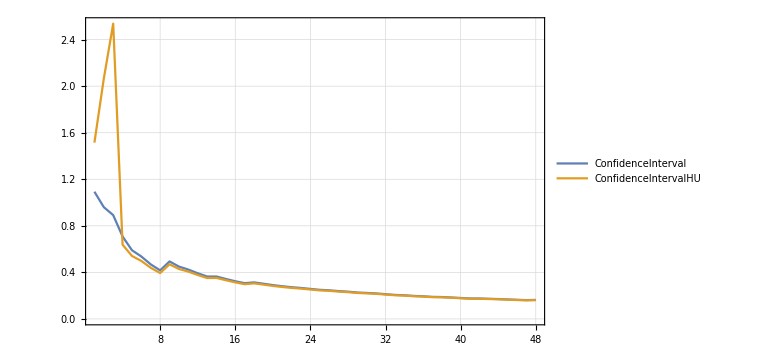

```mathematica
data=RandomVariate[NormalDistribution[0,1],50]; (*zufällige Daten erzeugen*)
ListLinePlot[Transpose[{ConfidenceInterval[data[[1;;#]]],ConfidenceIntervalHU[data[[1;;#]]]}&/@Range[3,50]],PlotRange->All,PlotTheme->"Detailed",ImageSize->Large,PlotLegends->{"ConfidenceInterval","ConfidenceIntervalHU"}]
```

## CalculateMeasurement & CalculateMeasurementHU

```mathematica
?CalculateMeasurement
```

CalculateMeasurement[{v1,v2,...},{e1,e2*C,...}] calculates a whole measurement with statistic uncertanty.
CalculateMeasurement[{v1,v2,...},{e1,e2*C,...},esys] calculates a whole measurement with statistic uncertanty and a systematic error.
CalculateMeasurement[{v1,v2,...},{e1,e2*C,...},esys,Analyze->True] calculates a whole measurement with statistic uncertanty, a systematic error and analyzes the result.

```mathematica
?CalculateMeasurementHU
```

CalculateMeasurement[{v1,v2,...},{e1,e2*C,...}] calculates a whole measurement with statistic uncertanty as defined in the HU-physics-practical.
CalculateMeasurement[{v1,v2,...},{e1,e2*C,...},esys] calculates a whole measurement with statistic uncertanty and a systematic error as defined in the HU-physics-practical.
CalculateMeasurement[{v1,v2,...},{e1,e2*C,...},esys,Analyze->True] calculates a whole measurement with statistic uncertanty, a systematic error as defined in the HU-physics-practical and analyzes the result.

CalculateMeasurement ist die drittwichtigste Funktion in diesem Package (zumindest meiner Meinung nach).
Es berechnet einen Messwert unter voller Berechnung der angegebenen Unsicherheiten, der statistischen Unsicherheit (Vertrauensbereich) und evtl. dem systematischen Fehler.
Aber fangen wir kleinschrittig an:

Die kleinste Form des Befehls nimmt nur Messwerte entgegen, berechnet den Mittelwert und nur die statistische Unsicherheit (Vertrauensbereich).

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1}]
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{}]
```

{4.99167,0.054435}

{4.99167,0.054435}

Man kann in der zweiten Liste nun eine konstante Unsicherheit einführen (z.B. Ableseunsicherheit) .
Hier eine konstante Unsicherheit von 0.5:

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5}]
```

{4.99167,0.502954}

Gleiches Beispiel, mehrere Unsicherheiten (0.5,1.5,0.75):

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,1.5,0.75}]
```

{4.99167,1.75085}

Manche Unsicherheiten, wie zum Beispiel Geräteunsicherheiten von digitalen Messgeräten, haben eine Prozentangabe vom gemessenen Mittelwert. Dieser kann in der Liste mit dem Wert C angeben werden.
Zum Beispiel: (konste Unsicherheit: 0.5 - Geräteunsicherheit: 0.4+1%·x̄)

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C}]
```

{4.99167,0.674825}

Man kann mit diesem Befehl ebenfalls einen systematische Fehler korrigieren lassen.
Zum Beispiel: u_sys=+0.6

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C},+0.6]
```

{5.59167,0.67884}

CalculateMeasurement ist ebenfalls der erste Befehl, mit der Analyse - Option, die eine genau Analyse der Daten anfertigt, die wichtig sind :

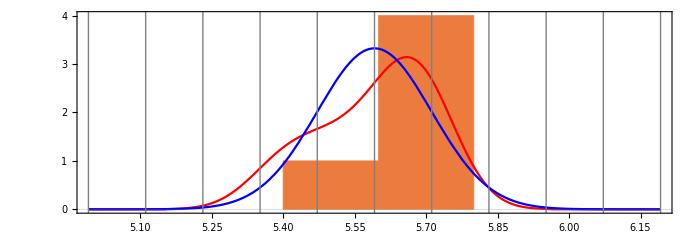
x̄ | u_sys | x̄+u_sys | u | u_sys/x̄ [%] | n | n_+ | n_- | n_0 | |n_+-n_-|≤√n | t | σ | min_i |x̄-x_i| | max_i |x̄-x_i|
4.99167 | 0.6 | 5.59167 | 0.67884 | 12.02 | 6 | 2 | 4 | 0 | 2≤2.44949 | 1.11051 | 0.120069 | 0.00833333 | 0.191667
uncertanity u | s̄=t·s/√n | 0.5 | 0.4+0.01 C
N[u] | 0.054435 | 0.5 | 0.455917
u^2 | 0.00296317 | 0.25 | 0.20786
uncertanty weight [%] | 0.643016 | 54.2507 | 45.1062
Sqrt-uncertanty weights [%] | 0.309024 | 52.1442 | 47.5468
-Graphics-

{5.59167,0.67884}

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C},+0.6,Analyze->True]
```

CalculateMeasurementHU ist der äquivalente Befehl, der die Definition des Vertrauensbereichs des HU Physik Praktikums benutzt.

## WeightedMean

```mathematica
?WeightedMean
```

WeightedMean[{{p1,e1},...}] calculates the weighted mean of a list.
WeightedMean[{{p1,e1},...},Analyze->True] calculates the weighted mean of a list and analyzes the result.

Dieser Befehl führt ein gewichtetes Mittel durch. Dabei muss dem Befehl eine Liste übergeben werden. Jedes Element dieser Liste ist wiederrum eine Liste mit zwei Einträgen. Der erste Eintrag ist der Wert, der zweite die zugeordnete Unsicherheit.
Beispiel:

g_1=(9.81±0.03)m/s^2
g_2=(9.79±0.11)m/s^2
g_3=(9.80±0.04)m/s^2
g_4=(9.6±0.7)m/s^2

```mathematica
WeightedMean[{{9.81,0.03},{9.79,0.11},{9.80,0.04},{9.6,0.7}}]
```

{9.80542,0.0234352}

Der Befehl warnt euch, wenn sich die Unsicherheitsintervalle nicht überschneiden :

```mathematica
WeightedMean[{{9.81,0.03},{9.59,0.11},{9.80,0.04},{9.6,0.7}}]
```

{9.79635,0.0234352}

Auch dieser Befehl kennt die Analyse option :

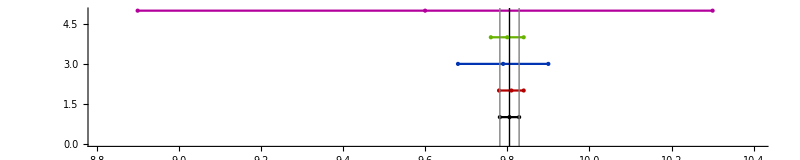
x̄ | ū | Σ p | Σ p·x
9.80542 | 0.0234352 | 1820.8 | 17853.7
values x | 9.81 | 9.79 | 9.8 | 9.6
uncertanties u | 0.03 | 0.11 | 0.04 | 0.7
weights p | 1111.11 | 82.6446 | 625. | 2.04082
weight-portion [%] | 61.0234 | 4.53893 | 34.3256 | 0.112084
p·x | 10900. | 809.091 | 6125. | 19.5918
p·x [%] | 61.0518 | 4.53179 | 34.3066 | 0.109736
Sqrt-p·x [%] | 48.4388 | 13.1971 | 36.3105 | 2.05361
-Graphics-

{9.80542,0.0234352}

```mathematica
WeightedMean[{{9.81,0.03},{9.79,0.11},{9.80,0.04},{9.6,0.7}},Analyze->True]
```

## RoundedErrorForm

```mathematica
?RoundedErrorForm
```

RoundedErrorForm[{value,error}] returns the rounded error form of a value with its uncertanty.

RoundedErrorForm berechnet die gerundete Darstellung eines Wertes mit seiner Unsicherheit. Er achtet dabei auf signifikante Stellen und DIN. Die Ausgabe erfolgt standartmäßig als String.

```mathematica
RoundedErrorForm[145.34,4.6]
```

(1.45±0.05)10

```mathematica
RoundedErrorForm[0.04567,0.00279]
```

(4.57±0.28)10

Die Ausgabe kann in eine Liste mit numerischen Werten erfolgen:

```mathematica
RoundedErrorForm[0.04567,0.00279,Form->Null]
RoundedErrorForm[0.04567,0.00279,Form->Null]//N
```

{457/10000,7/2500}

{0.0457,0.0028}

Der Befehl kann auch LaTeX code ausgeben :

```mathematica
RoundedErrorForm[0.04567,0.00279,Form->"latex"]
```

\left(4.57\pm0.28\right)10^{-2}

## ErrorProbability

```mathematica
?ErrorProbability
```

ErrorProbability[dof, χP] calculates the error probability for a given degrees of freedom dof and chi-squared-value χP.

ErrorProbability berechnet die Irrtumswahrscheinlichkeit aus den χ^2-Test und den Freiheitsgraden

```mathematica
ErrorProbability[10,2.56]
ErrorProbability[8,7.34]
```

0.989972

0.500432

Exakte Argumente werden auch exakt ausgewertet:

```mathematica
ErrorProbability[20,3]
```

1-GammaRegularized[10,0,3/2]

## GaussianErrorPropagation

```mathematica
?GaussianErrorPropagation
```

GaussianErrorPropagation[function] returns the function and gaussian error propagation.
GaussianErrorPropagation[function,{{p1,v1,e1},{p2,v2},p3,...}] calculates the function and gaussian error propagation given via the parameters.
GaussianErrorPropagation[function,{{p1,v1,e1},{p2,v2},p3},Analyze->True] calculates the function and gaussian error propagation given via the parameters and analyzes the result.

Der zweitwichtigste Befehl in diesem Package. Die automatische Gaußsche Fehlerfortpflanzung.
In der einfachsten Darstellung, berechnet der Befehl nur die Formel.

```mathematica
GaussianErrorPropagation[a*x/c+d]
```

{d+(a x)/c,√((x^2 C[a]^2)/c^2+(a^2 x^2 C[c]^2)/c^4+C[d]^2+(a^2 C[x]^2)/c^2)}

Im zweiten Argument, listet man die Variablen mit ihren Werten und Unsicherheiten auf.

a=(50.0±0.1)
d=(8.1±0.9)

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9}}]
```

{6.17284,0.685982}

Kovarianzen zwischen Variablen werden in einer Liste mit den zwei Variablen und der Kovarianc angegeben.

u_(a,d)=0.5

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9},{a,d,0.5}}]
```

{6.17284,0.613586}

Keine der Listen muss völlig ausgefüllt sein (beachte, dass x keine Unsicherheitsbehaftet größe ist, wenn sie nicht explizit angegeben wird):

```mathematica
GaussianErrorPropagation[a*x/c+d,{a,{d,1},{c,5,0.1},{a,c},{a,d,0.5}}]
```

{1+(a x)/5,√(0.2 x+0.000016 a^2 x^2+1/25 x^2 C[a]^2+C[d]^2-2/125 a x^2 C[a,c])}

Auch dieser Befehl, kennt die Analyse Option.

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9},{a,d,0.5}},Analyze->True]
```

Parameters | {{a,50,0.1},{d,8.1,0.9},{a,d,0.5}}
Function | Uncertanty
a/d | √(C[a]^2/d^2+(a^2 C[d]^2)/d^4-(2 a C[a,d])/d^3)
6.17284 | 0.613586
Type/Variable | Formula | Value | Weights [%] | Relative Weights [%] | Sqrt-Weights [%]
C[a] | C[a]^2/d^2 | 0.000152416 | 0.0269927 | 0.0404836 | 1.22849
C[d] | (a^2 C[d]^2)/d^4 | 0.470419 | 83.3108 | 124.949 | 68.2494
C[a,d] | -(2 a C[a,d])/d^3 | -0.0940838 | -16.6622 | -24.9899 | -30.5221

{6.17284,0.613586}

Der Befehl ist ebenfalls in der Lage, Daten aus FittedModel - Objekten zu ziehen.
Dazu müssen zu allererst fits erstellt werden.

```mathematica
data=Table[{x,-20*x^2-x+1+RandomReal[]},{x,0,10,0.5}];
linearFit=LinearModelFit[data,{x^2,x,1},x]
nonlinearFit=NonlinearModelFit[data,a*x^2+b*x+c,{a,b,c},x]
```

FittedModel[1.51678-0.983238 x-20.0031 x^2]

FittedModel[1.51678-0.983238 x-20.0031 x^2]

Wie erklärt, erstellt Mathematica bei jedem Fit, ein FittedModel - Objekt. Dabei ist wichtig anzumerken:
LINEARE FITS UND NICHTLINEARE FITS ERZUEGEN UNTERSCHIEDLICHE FITTEDMODEL - OBJEKTE
Ich halte es kurz und sage nur, dass in Nichtlinearen-FittedModel-Objekte Informationen über Variablennamen enthalten ist.
Dadurch kann der Befehl leicht diese Objekte benutzen.
Es werden sämtliche Variablen und Kovarianzen berücksichtigt.

```mathematica
GaussianErrorPropagation[a/b+c,{nonlinearFit}]
```

{21.8609,1.66191}

Bei linearen fits, muss noch die Variablenstruktur mit angegeben werden :

```mathematica
GaussianErrorPropagation[a/b+c,{{linearFit,{a,b,c}}}]
```

{21.8609,1.66191}

Das kann natürlich auch gemischt angewendet werden.

```mathematica
GaussianErrorPropagation[a/b+c^d,{nonlinearFit,{d,2,0.1}}]
```

{22.6448,1.37499}

Und auch analysiert werden

```mathematica
GaussianErrorPropagation[a/b+c^d,{nonlinearFit,{d,2,0.1}},Analyze->True]
```

Parameters | {{a,-20.0031,0.00844144},{b,-0.983238,0.0874345},{c,1.51678,0.18867},{a,b,-0.000712579},{a,c,0.00112825},{b,c,-0.0138775},{d,2,0.1}}
Function | Uncertanty
a/b+c^d | √(C[a]^2/b^2+(a^2 C[b]^2)/b^4+c^(-2+2 d) d^2 C[c]^2-(2 a C[a,b])/b^3+(2 c^(-1+d) d C[a,c])/b-(2 a c^(-1+d) d C[b,c])/b^2+c^(2 d) C[d]^2 Log[c]^2)
22.6448 | 1.37499
Type/Variable | Formula | Value | Weights [%] | Relative Weights [%] | Sqrt-Weights [%]
C[a] | C[a]^2/b^2 | 0.0000737081 | 0.00136782 | 0.00389864 | 0.211338
C[b] | (a^2 C[b]^2)/b^4 | 3.27285 | 60.735 | 173.111 | 44.5331
C[c] | c^(-2+2 d) d^2 C[c]^2 | 0.327575 | 6.07887 | 17.3264 | 14.0888
C[a,b] | -(2 a C[a,b])/b^3 | 0.0299906 | 0.556542 | 1.58629 | 4.26297
C[a,c] | (2 c^(-1+d) d C[a,c])/b | -0.00696192 | -0.129194 | -0.368237 | -2.05393
C[b,c] | -(2 a c^(-1+d) d C[b,c])/b^2 | -1.7421 | -32.3286 | -92.145 | -32.4905
C[d] | c^(2 d) C[d]^2 Log[c]^2 | 0.00918561 | 0.170459 | 0.485855 | 2.35925

{22.6448,1.37499}

## AdaptiveNonlinearModelFit

```mathematica
?AdaptiveNonlinearModelFit
```

AdaptiveNonlinearModelFit[data,form,parameters,x] constructs a nonlinear model to fit the form to the given data while trying to choose appropriate starting values.

Um einen nichtlinearen Fit in Mathematica auszuführen, benutzt man den Befehl NonlinearModelFit.
Wie aber für nichtlineare Fits üblich, besteht die Gefahr, dass diese Fits bei ungeeigneter Wahl der Startparameter nicht konvergieren. 
Nun wäre es aber wünschenswert wenn die Funktion selbstständig Startparameter wählen könnte um den Fit zu begünstigen. 
Dafür enthält dieses package den Befehl AdaptiveNonlinearModelFit. Die Syntax ist die gleiche wie beim normalen NonlinearModelFit.

#### Achtung:

Dieser Befehl ist experimentell. Ich habe eine lange Zeit verbracht die Methoden für diesen Befehl zu generalisieren sodass sie möglichst viele Fitmodelle verarbeiten könnten. Trotzdem ist das kein Garant dafür, dass der Fit konvergiert.
Desweiteren muss beachtet werden, dass der Befehl im inneren massive Algebraische Operationen ausführt. Demnach kann es sein, dass diese Funktion mehrere Sekunden, Minuten oder sogar länger braucht. Die längste gemessene Zeit dieser Funktion liegt bei ungefähr 10Minuten für ein Fitmodell mit 6 Parametern zur Bestimmung der Autokorrelationsfunktion einer Quantenkorrelation. Üblich sind aber nur 2-3 Sekunden für einfachere Modelle.
Trotzdem: seit bereit nichtsdestotrotz selber Startwerte für komplizierte Probleme bereitzustellen.

Zum testen erstellen wir drei Test-Datensätze (die natürlich so von mir gewählt worden sind, dass NonlinearModelFit ohne Wahl der Startparameter nicht konvergiert):

```mathematica
adata1={{1,10001.8},{2,10000.8},{3,9999.89},{4,9999.53},{5,9999.73},{6,10000.1},{7,10000.3},{8,10000.2},{9,9999.89},{10,9999.8},{11,9999.91},{12,10000.1},{13,10000.2},{14,10000.1},{15,9999.9},{16,9999.88},{17,9999.99},{18,10000.1},{19,10000.1},{20,10000.},{21,9999.92},{22,9999.92},{23,10000.},{24,10000.1},{25,10000.1},{26,9999.97},{27,9999.92},{28,9999.95},{29,10000.},{30,10000.1}};
adata2={{-3.01,-33},{-2.6,-34},{-2.2,-33},{-1.8,-26},{-1.7,-20},{-1.6,-12},{-1.5,0},{-1.4,20},{-1.3,61}};
wdata2={6.98467,14.3664,6.90228,5.30757,4.61407,6.94984,14.9547,14.4406,3.68319};
adata3=(#+{0,10000}&)/@{{0.1,0.0898647},{0.2,-0.0535735},{0.3,-0.148313},{0.4,0.0846445},{0.5,0.09901},{0.6,-0.074521},{0.7,-0.142624},{0.8,-0.0864354},{0.9,-0.0212738},{1.,0.0221625},{1.1,0.105401},{1.2,-0.0966202},{1.3,0.0877835},{1.4,0.0789275},{1.5,0.015885},{1.6,0.118934},{1.7,0.04146},{1.8,0.0344122},{1.9,0.054369},{2.,0.127307},{2.1,0.120975},{2.2,0.0272045},{2.3,0.102872},{2.4,0.11786},{2.5,-0.122479},{2.6,-0.109226},{2.7,-0.110917},{2.8,0.0986023},{2.9,-0.0694651},{3.,0.084825},{3.1,0.0369083},{3.2,0.197759},{3.3,0.138431},{3.4,0.321953},{3.5,0.360677},{3.6,0.27348},{3.7,0.441175},{3.8,0.407004},{3.9,0.359329},{4.,0.418597},{4.1,0.552704},{4.2,0.525389},{4.3,0.528137},{4.4,0.224216},{4.5,0.436397},{4.6,0.389716},{4.7,0.326866},{4.8,0.108578},{4.9,0.225344},{5.,0.0938303}};
```

#### Beispieldatensatz 1: versetzte, abklingende Schwingung

Dieser Datensatz konvergiert in beiden Fällen. AdaptiveNonlinearModelFit kann aber von Anfang an, den c-Parameter wählen, wodurch die anderen Parameter nichtmehr groß schwanken müssen um ins globale Minimum zu konvergieren.
NonlinearModelFit hingegen braucht sehr viele Schritte bis der c-Parameter angepasst ist wodurch die Parameter a und b weit driften und die Funktion somit in ein lokales Minimum konvergiert welches, wie im Plot zu sehen, aber eine viel zu große Frequenz aufweist.

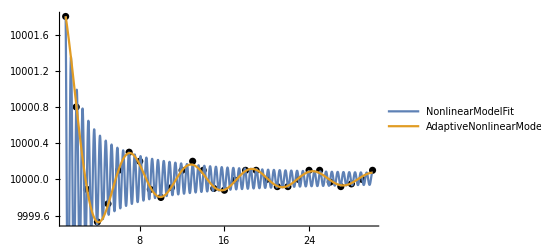

```mathematica
fit1=NonlinearModelFit[adata1,a*Sin[b*x]/x+c,{a,b,c},x];
afit1=AdaptiveNonlinearModelFit[adata1,a*Sin[b*x]/x+c,{a,b,c},x];
Show[ListPlot[adata1,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit1["BestFit"],afit1["BestFit"]},{x,1,30},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

#### Beispieldatensatz 2: Photostrom im äußeren Photoeffekt

Dies ist ein Realer Datensatz vom Versuch A1-Photoeffekt. Man sieht leicht, dass NonlinearModelFit sich in einem lokalen Minimum gefangen hat, dass realisiert und eine Fehlermeldung ausgibt. 
AdaptiveNonlinearModelFit kann von Anfang an aber a und b wählen wodurch nurnoch c gefunden werden muss.

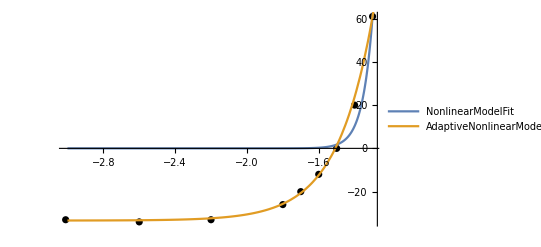

```mathematica
fit2=NonlinearModelFit[adata2,a*(Exp[(u-b)/c]-1),{a,b,c},u,Weights->1/wdata2^2,MaxIterations->10000];
afit2=AdaptiveNonlinearModelFit[adata2,a*(Exp[(u-b)/c]-1),{a,b,c},u,Weights->1/wdata2^2];
Show[ListPlot[adata2,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit2["BestFit"],afit2["BestFit"]},{u,-3,-1},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

#### Beispieldatensatz 3: verschobene Normalverteilung mit stark rauschenden Daten

Auch hier merkt NonlinearModelFit, dass es nicht konvergiert ist aber dagegen nichts tun kann.
AdaptiveNonlinearModelFit kann selbst aus diesen schlechten Daten die Parameter A, x0 und o wählen wodurch nurnoch eta gefunden werden muss.

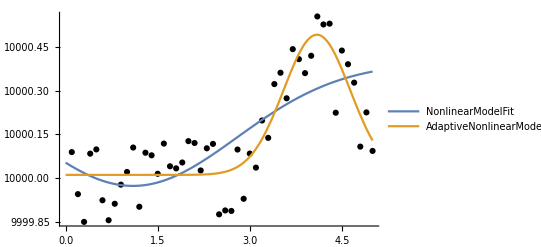

```mathematica
fit3=NonlinearModelFit[adata3,A*Exp[-(x-x0)^2/eta]+o,{A,x0,eta,o},x,MaxIterations->10000];
afit3=AdaptiveNonlinearModelFit[adata3,A*Exp[-(x-x0)^2/eta]+o,{A,x0,eta,o},x];
Show[ListPlot[adata3,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit3["BestFit"],afit3["BestFit"]},{x,0,5},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

## FitPlot

```mathematica
?FitPlot
```

FitPlot[data,xErrors,yErrors,equations,variables,xLabel,yLabel,legendPosition] performs weighted equation-fits on data according to the variables and plots the result with labels and legends.
FitPlot[data,equations,variables] performs equation-fits on data according to the variables and plots the result.
FitPlot[data,yErrors,equations,variables] performs weighted equation-fits on data according to the variables and plots the result.
FitPlot[data,xErrors,yErrors,equations,variables] performs weighted equation-fits on data according to the variables and plots the result.
FitPlot[data,equations,variables,xLabel,yLabel] performs equation-fits on data according to the variables and plots the result with labels.
FitPlot[data,equations,variables,xLabel,yLabel,legendPosition] performs equation-fits on data according to the variables and plots the result with labels and legends.
FitPlot[data,yErrors,equations,variables,xLabel,yLabel,legendPosition] performs weighted equation-fits on data according to the variables and plots the result with labels and legends.

#### Der Befehl, für den dieses Package überhaupt existiert. Wir erzeugen erstmal Daten.

```mathematica
n=20;
xErrors=0.05+Abs@RandomVariate[NormalDistribution[0,0.05],n];
yErrors=RandomVariate[NormalDistribution[0,0.3],n];
data=Table[{i/n*5,0.2*(i/n*5)^2-2*i/n*5+yErrors[[i]]},{i,1,n}];
yErrors=0.2+Abs@yErrors;
```

#### Nun benutzen wir den Befehl in seiner einfachsten Form:

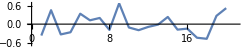
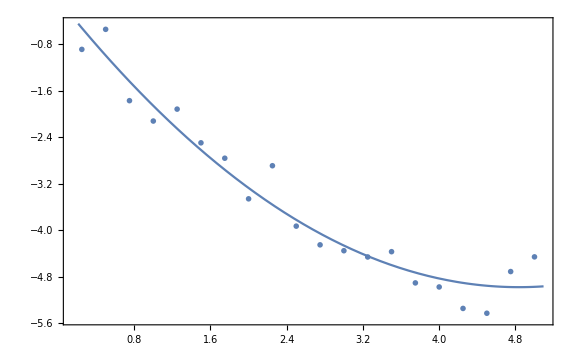
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.02278 | 0.260478 | 0.931332 | c
b | -2.04904 | 0.228507 | 7.46503×10^-8 | b
a | 0.211783 | 0.0422782 | 0.000107472 | a
model-object | FittedModel[-0.02278-2.04904 x+0.211783 x^2]
{χ^2/dof,α} | {0.122579,0.726254}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.949984,0.9441}
{77.6358,76.3568}
correlations |  | c | b | a | 
c | 1. | -0.888805 | 0.781116 | c
b | -0.888805 | 1. | -0.971348 | b
a | 0.781116 | -0.971348 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0678488 | -0.0529027 | 0.00860207 | c
b | -0.0529027 | 0.0522157 | -0.00938407 | b
a | 0.00860207 | -0.00938407 | 0.00178744 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,a*x^2+b*x+c,x]
```

#### Mit Fehlerbalken :

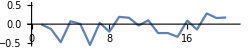
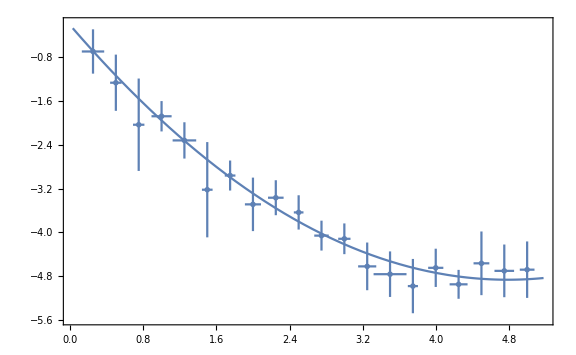
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,xErrors,yErrors,a*x^2+b*x+c,x]
```

#### Und den restlichen Parametern

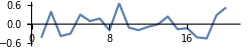
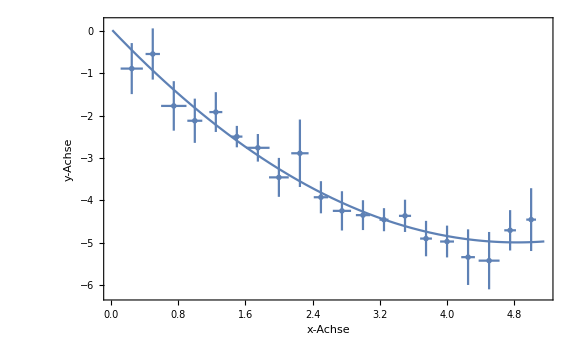
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | 0.0566011 | 0.244119 | 0.819416 | c
b | -2.09166 | 0.204438 | 1.10622×10^-8 | b
a | 0.216461 | 0.0382138 | 0.0000279815 | a
model-object | FittedModel[0.0566011-2.09166 x+0.216461 x^2]
{χ^2/dof,α} | {0.363023,0.546832}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.963346,0.959033}
{80.8547,79.7598}
correlations |  | c | b | a | 
c | 1. | -0.926426 | 0.83278 | c
b | -0.926426 | 1. | -0.972755 | b
a | 0.83278 | -0.972755 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0595939 | -0.0462353 | 0.00776875 | c
b | -0.0462353 | 0.0417949 | -0.0075995 | b
a | 0.00776875 | -0.0075995 | 0.00146029 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,xErrors,yErrors,a*x^2+b*x+c,x,"x-Achse","y-Achse",{3.2,0.4}]
```

#### Davon kann man sich erst erschlagen fühlen, aber wir fangen es langsam an. Als erstes alle Standardparameter :

```mathematica
FitPlot[
data (*Daten die gefittet werden sollen in Punktlisten {{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...} oder zu mehreren Fits {{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...},{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...},...}*)
,xErrors (*die x Fehler in Einfachlisten {Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...} oder Mehrfachlisten {{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},...}*)
,yErrors (*die y Fehler in Einfachlisten {Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...} oder Mehrfachlisten {{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},...}*)
,equations (*die Gleichungen, nach denen gefittet wird. Wenn nur eine Gleichung gefittet wird, braucht es keine Liste*)
,variables (*die Funktionsvariablen der Gleichungen. Wird nur ein Fit gemacht, braucht es keine Liste*)
,xLabel (*das x-Achsenlabel als string also mit Anführungszeichen*)
,yLabel (*das y-Achsenlabel als string also mit Anführungszeichen*)
,legendPosition (*die Position der legende. Eine leere Liste {} stellt die Legende neben den Plot, Null entfernt sie komplett oder ein Punkt {x,y} positioniert sie mit der linken oberen Ecke in diesen Punkt*)
]
```

FitPlot[{{1/4,-0.692716},{1/2,-1.26416},{3/4,-2.03259},{1,-1.87754},{5/4,-2.31941},{3/2,-3.2213},{7/4,-2.96187},{2,-3.48913},{9/4,-3.36767},{5/2,-3.63639},{11/4,-4.0609},{3,-4.11901},{13/4,-4.62358},{7/2,-4.76633},{15/4,-4.98415},{4,-4.65012},{17/4,-4.95187},{9/2,-4.56768},{19/4,-4.70565},{5,-4.68379}},{0.122382,0.0627865,0.0622871,0.109928,0.128946,0.0582122,0.0581601,0.0879503,0.0852496,0.0526804,0.0791673,0.0672273,0.0991632,0.18014,0.0554229,0.0830507,0.0981263,0.0863549,0.107287,0.0804867},{0.405216,0.514159,0.84509,0.27754,0.331907,0.871303,0.274371,0.489133,0.319829,0.313614,0.273395,0.280994,0.436084,0.416332,0.496646,0.349881,0.264372,0.582321,0.481855,0.516214},equations,variables,xLabel,yLabel,legendPosition]

#### Was bedeutet nun also die Tabelle neben dem Plot? Das ist die Auswertungstabelle. Hier nochmal :

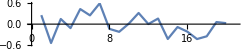
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | 0.167699 | 0.177309 | 0.357502 | c
b | -2.11643 | 0.134374 | 1.4236×10^-11 | b
a | 0.214673 | 0.0222668 | 2.63896×10^-8 | a
model-object | FittedModel[0.167699-2.11643 x+0.214673 x^2]
{χ^2/dof,α} | {0.295409,0.586775}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982148,0.980048}
{86.6388,85.8747}
correlations |  | c | b | a | 
c | 1. | -0.92013 | 0.82979 | c
b | -0.92013 | 1. | -0.97583 | b
a | 0.82979 | -0.97583 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0314386 | -0.0219228 | 0.0032761 | c
b | -0.0219228 | 0.0180563 | -0.00291975 | b
a | 0.0032761 | -0.00291975 | 0.000495809 | a
 | c | b | a | 
residuals | -Graphics-

#### In Reihenfolge :

regression: Als erstes sehen wir hier die Farbige Linie. Diese zeigt euch an, welche Farbe die Regression im Plot hat. 
Desweiteren findet ihr daneben noch eine Beschreibung. Möglichkeiten dafür sind: {polynomial linear, nonlinear, adaptive nonlinear, single linear, multi-combination linear}.
Diese Beschreibungen geben euch an, was der Befehl im “inneren” mit euren Fit-Modell angestellt hat. Wie ihr ja wissen solltet, kann eine Regression linear oder nichtlinear ablaufen.
Dabei gilt, dass linear immer besser ist als nichtlinear, da hier die Gefahr der nicht-Konvergenz nicht besteht. FitPlot versucht also nun euer angegebenes Fitmodell zu analysieren.
Wenn eure Gleichung ohne große Änderungen als Polynom dargstellt werden kann, dass einem linearen Fit genügt, wird eure Funktion im inneren danach umgestellt und die jeweilig nötigen
Funktionen und Parameter extrahiert und linear regressiert. Das wird dargstellt mit “polynomial linear”
single linear und multi-combination linear sind Namen für Gleichungen die als lineares Fitmodell aber nicht als Polynom dargestellt werden können. Hierbei werden aber scheinbar offensichtliche
Vereinfachungen NICHT gemacht also wenn ihr unbedingt linear fitten wollt, müsst ihr eure Gleichung selbstständig linearisieren.
nonlinear ist demnach einfach die Option bei der kein lineares Fitmodell extrahiert werden konnte und es wird nichtlinear regressiert. adaptive nonlinear benutzt den AdaptiveNonlinearModelFit dieses Packages um eine Konvergenz wahrscheinlicher zu machen.

equation: wie man sich denken kann, wird hier nochmal das Fitmodell dargstellt (nicht vereinfacht). Wenn hier eine Liste mit zwei Gleichungen angegeben wird, dann weil ein Parameter umbenannt wurde (weiteres dazu später).

parameters: Hier wird die Parameter-Tabelle dargstellt. Hier bekommt ihr euren internen Variablennamen, die Abschätzung des Wertes, der Unsicherheit, den statistischen P-Wert und den Darstellungsname der Variable.
Der P-Wert ist bei statistisch signifikanten Werten als Faustregel unter 0.05. Sollte ein Parameter das nicht erfüllen, wird die Zeile in Rot dargstellt.

model-object: Bei jeder Regression erzeugt Mathematica ein FittedModel-Objekt. Meistens unnötig für euch aber wenn ihr Zusatzinfos braucht die euch hier nicht angezeigt werden, dann daraus.

{χ^2/dof,α}: Der erste Wert der Liste ist der χ^2/dof Wert. Der zweite ist die zugehörige Irrtumswahrscheinlichkeit α. Die Farbe kann von grün (alles okay) zu orange (mäßige Irrtumswahrscheinlichkeit) bis rot (große Irrtumswahrscheinlichkeit) gehen.

{R^2,(R̄)^2}
{R^2%,(R̄)^2%} : R^2 ist der normale R-Quadrat Test und (R̄)^2 ist der angepasste Test. Die Prozentangaben darunter sind die prozentualen Erklärungen der Abweichungen zur Standardabweichung. (http://people.duke.edu/~rnau/rsquared.htm)
Auch hier ist eine Farbliche angabe von grün zu orange bis rot ein Indikator für die Erklärung der Standardabweichung (berechnet aus den erklärten Standartabweichungen des (R̄)^2%).

correlations: Korrelationsmatrix zur Abschätzung der Korrelationen

covariances: Kovarianzmatrix für die korrelierte Gaußsche Fehlerfortpflanzung

residuals: Die Residuuen des Fits. Diese werden nur angezeigt, wenn die Residual-Option auf False steht.

#### Die Funktion versteht sich im Input auch auf meherere Datensätze:

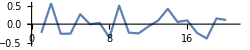
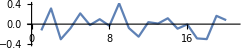
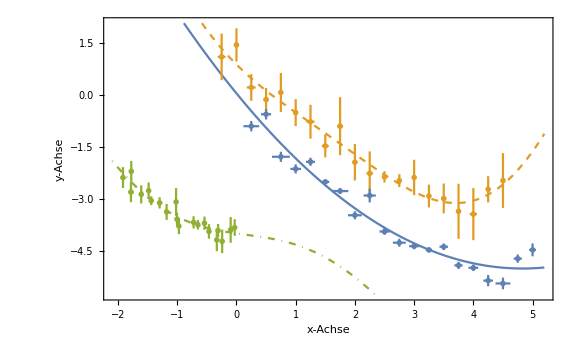
regression |  |  | 
equation | a x^2+b x+c | f sin(y)+q y^2+r+w y | a w^2+b w+c+sin(w)
parameters |  | value | error | p-value | 
c | 0.0566011 | 0.244119 | 0.819416 | c
b | -2.09166 | 0.204438 | 1.10622×10^-8 | b
a | 0.216461 | 0.0382138 | 0.0000279815 | a |  | value | error | p-value | 
r | 0.889151 | 0.161102 | 0.0000466705 | r
w | -2.72075 | 0.406017 | 5.09103×10^-6 | w
q | 0.482737 | 0.119618 | 0.000957491 | q
f | 1.01585 | 0.425943 | 0.0297982 | f |  | value | error | p-value | 
c | -3.98411 | 0.114811 | 3.19309×10^-17 | c
b | -1.24494 | 0.269606 | 0.000245656 | b
a | 0.0791922 | 0.136671 | 0.569895 | a
model-object | FittedModel[0.0566011-2.09166 x+0.216461 x^2] | FittedModel[0.889151-2.72075 y+0.482737 y^2+1.01585 Sin[y]] | FittedModel[-3.98411-1.24494 w+0.0791922 w^2+Sin[w]]
{χ^2/dof,α} | {5.80836,0.0159501} | {0.0960833,0.756581} | {0.49975,1.}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.963346,0.959033}
{80.8547,79.7598} | {0.963102,0.956183}
{80.791,79.0675} | {0.998402,0.99812}
{96.0026,95.6642}
correlations |  | c | b | a | 
c | 1. | -0.926426 | 0.83278 | c
b | -0.926426 | 1. | -0.972755 | b
a | 0.83278 | -0.972755 | 1. | a
 | c | b | a |  |  | r | w | q | f | 
r | 1. | -0.0203571 | -0.11076 | -0.303207 | r
w | -0.0203571 | 1. | -0.989178 | -0.912393 | w
q | -0.11076 | -0.989178 | 1. | 0.949779 | q
f | -0.303207 | -0.912393 | 0.949779 | 1. | f
 | r | w | q | f |  |  | c | b | a | 
c | 1. | 0.89425 | 0.783547 | c
b | 0.89425 | 1. | 0.969401 | b
a | 0.783547 | 0.969401 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0595939 | -0.0462353 | 0.00776875 | c
b | -0.0462353 | 0.0417949 | -0.0075995 | b
a | 0.00776875 | -0.0075995 | 0.00146029 | a
 | c | b | a |  |  | r | w | q | f | 
r | 0.0259537 | -0.00133156 | -0.0021344 | -0.0208061 | r
w | -0.00133156 | 0.16485 | -0.0480412 | -0.15779 | w
q | -0.0021344 | -0.0480412 | 0.0143084 | 0.0483915 | q
f | -0.0208061 | -0.15779 | 0.0483915 | 0.181428 | f
 | r | w | q | f |  |  | c | b | a | 
c | 0.0131816 | 0.0276804 | 0.0122949 | c
b | 0.0276804 | 0.0726874 | 0.0357199 | b
a | 0.0122949 | 0.0357199 | 0.018679 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics- | -Graphics-
not saved (no file specified)
-Graphics-

```mathematica
FitPlot[
{data,data+ConstantArray[{-0.5,2},Length[data]],0.4*data-2+0.1*RandomReal[{-1,1},Length[data]]},
{xErrors,0.5*xErrors,0.3*xErrors},
{0.25*yErrors,yErrors+0.2*RandomReal[{-1,1},Length[data]],0.5*yErrors},
{a*x^2+b*x+c,q*y^2+w*y+r+f*Sin[y],a*w^2+b*w+c+Sin[w]},
{x,y,w},
"x-Achse",
"y-Achse",
{}
]
```

#### Jetzt, da wir den Output und Input der Funktion verstehen, gucken wir uns noch Zusatzfunktionen des Befehls an: Die Funktion besitzt auch noch einige Optionen

```mathematica
Options[FitPlot]/.Rule[a_,_]:>a
```

{FunctionNames,PlotRange,InitialGuesses,AdaptiveNonlinearFit,Residuals,ParameterNames,GridLines,FileSave,Units,ExtraPlots,ExtraLegends,Analyze,RSquaredTest,ChiSquareTest,PlotMarkerSize}

#### Option: FunctionNames

Funktionsnamen lassen sich mit der Option FunctionNames ändern.
Im folgenden Beispiel ändern wir die Definition zu ω(x)

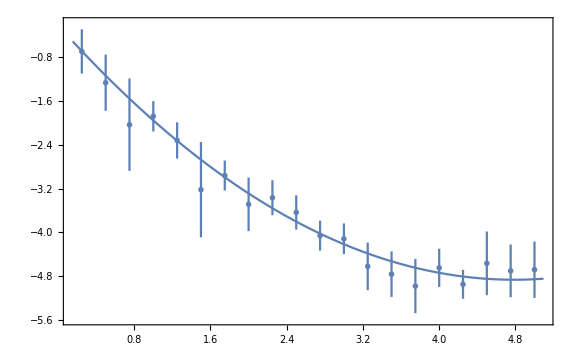
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
FunctionNames->{"ω(x)"}
]
```

#### Option: PlotRange

Die Option gibt euch die Möglichkeit eure PlotRange EXPLIZIT (kein Automatic o.Ä.) festzulegen

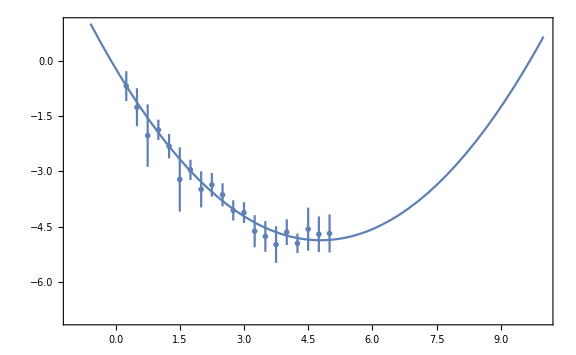
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotRange->{{-1,10},{-7,1}}
]
```

#### Option: InitialGuesses

Sollte eure Gleichung nichtlinear gefitted werden müssen, kann es sein, das ihr Startparameter wählen müsst damit die Funktion konvergiert.
Ein Beispiel:

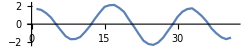
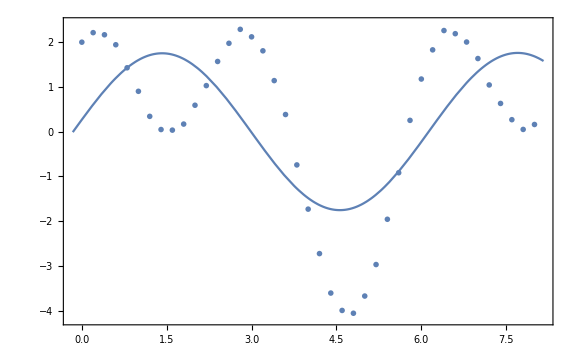
regression | 
equation | a sin(x)+b cos(c x)
parameters |  | value | error | p-value | 
b | 0.266197 | 0.330651 | 0.425789 | b
c | 0.995101 | 0.51256 | 0.0596482 | c
a | 1.7251 | 0.661483 | 0.0129488 | a
model-object | FittedModel[0.266197 Cos[0.995101 x]+1.7251 Sin[x]]
{χ^2/dof,α} | {2.16686,1.}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.444973,0.401155}
{25.4998,22.6149}
correlations |  | b | c | a | 
b | 1. | -0.052432 | -0.111957 | b
c | -0.052432 | 1. | 0.870641 | c
a | -0.111957 | 0.870641 | 1. | a
 | b | c | a | 
covariances |  | b | c | a | 
b | 0.10933 | -0.00888611 | -0.0244871 | b
c | -0.00888611 | 0.262718 | 0.29519 | c
a | -0.0244871 | 0.29519 | 0.437559 | a
 | b | c | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
dataIG=Table[{x,2*Sin[x]+2*Cos[x*2]+0.1*RandomReal[{-1,1}]},{x,0,8,0.2}]; (*zufällige Daten*)
FitPlot[dataIG,a*Sin[x]+b*Cos[c*x],x]
```

Wir sehen leicht, der Fit ist nicht ins globale Minimum konvergiert. Wenn wir nun aber nur einen einzigen Parameter vorwählen:

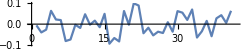
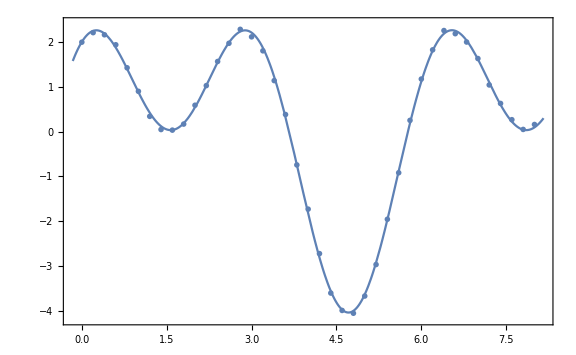
regression | 
equation | a sin(x)+b cos(c x)
parameters |  | value | error | p-value | 
b | 2.00094 | 0.0114452 | 7.86775×10^-57 | b
c | 1.9997 | 0.0013345 | 2.82122×10^-92 | c
a | 2.03467 | 0.011897 | 1.81354×10^-56 | a
model-object | FittedModel[2.00094 Cos[1.9997 x]+2.03467 Sin[x]]
{χ^2/dof,α} | {0.00273662,1.}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.999299,0.999244}
{97.3524,97.2499}
correlations |  | b | c | a | 
b | 1. | 0.00231622 | 0.132354 | b
c | 0.00231622 | 1. | 0.234638 | c
a | 0.132354 | 0.234638 | 1. | a
 | b | c | a | 
covariances |  | b | c | a | 
b | 0.000130992 | 3.53771×10^-8 | 0.0000180218 | b
c | 3.53771×10^-8 | 1.7809×10^-6 | 3.72526×10^-6 | c
a | 0.0000180218 | 3.72526×10^-6 | 0.000141539 | a
 | b | c | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[dataIG,a*Sin[x]+b*Cos[c*x],x,
InitialGuesses->{c->2}
]
```

konvergiert die Regression super.

#### Option: AdaptiveNonlinearFit

Hat man eine Funktion die nichtlinear gefittet werden muss, aber scheionbar nicht konvergiert, kann man diese Option auf True stellen, um einen AdaptiveNonlinearModelFit einzusetzen der versucht gute Startparameter zu wählen.

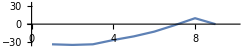
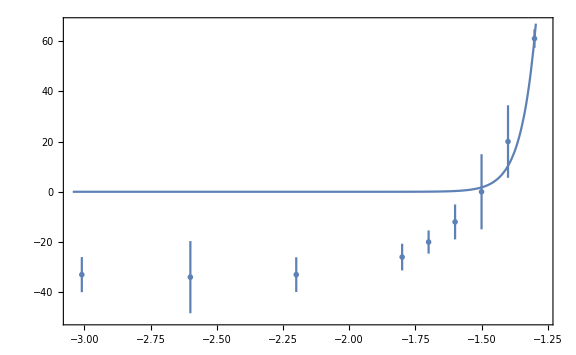
regression | 
equation | a (ⅇ^((u-b)/c)-1)
parameters |  | value | error | p-value | 
a | 3.58179×10^-7 | 10.6008 | 1. | a
c | 0.0562501 | 0.173996 | 0.75745 | c
b | -2.36618 | 1.66479×10^6 | 0.999999 | b
model-object | FittedModel[3.58179×10^-7 (-1+ⅇ^(17.7778 (2.36618+u)))]
{χ^2/dof,α} | {16.2115,0.0126628}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.739056,0.608584}
{48.9173,37.4367}
correlations |  | a | c | b | 
a | 1. | 0.282162 | 1. | a
c | 0.282162 | 1. | 0.28216 | c
b | 1. | 0.28216 | 1. | b
 | a | c | b | 
covariances |  | a | c | b | 
a | 112.376 | 0.520444 | 1.7648×10^7 | a
c | 0.520444 | 0.0302745 | 81732.2 | c
b | 1.7648×10^7 | 81732.2 | 2.77152×10^12 | b
 | a | c | b | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
adata2={{-3.01,-33},{-2.6,-34},{-2.2,-33},{-1.8,-26},{-1.7,-20},{-1.6,-12},{-1.5,0},{-1.4,20},{-1.3,61}};
wdata2={6.98467,14.3664,6.90228,5.30757,4.61407,6.94984,14.9547,14.4406,3.68319};
FitPlot[adata2,wdata2,a*(Exp[(u-b)/c]-1),u]
```

Wie erwartet, konvergiert der Fit nicht. Jetzt setzen wir die Option auf True:

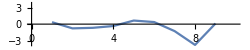
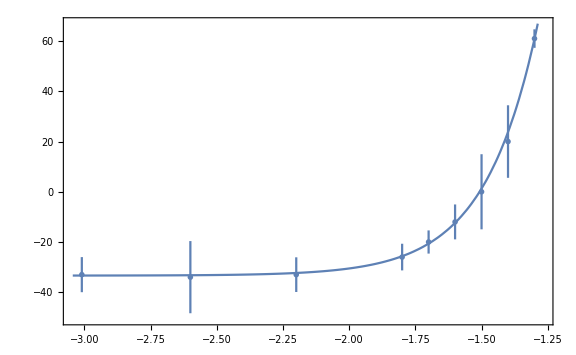
regression | 
equation | a (ⅇ^((u-b)/c)-1)
parameters |  | value | error | p-value | 
a | 33.3727 | 0.651066 | 3.69917×10^-9 | a
c | 0.19978 | 0.0054284 | 2.68528×10^-8 | c
b | -1.50743 | 0.00388653 | 1.98246×10^-14 | b
model-object | FittedModel[33.3727 (-1+ⅇ^(5.00552 (1.50743+u)))]
{χ^2/dof,α} | {0.0195968,1.}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.999685,0.999527}
{98.2239,97.8248}
correlations |  | a | c | b | 
a | 1. | 0.790776 | -0.487766 | a
c | 0.790776 | 1. | -0.893268 | c
b | -0.487766 | -0.893268 | 1. | b
 | a | c | b | 
covariances |  | a | c | b | 
a | 0.423887 | 0.0027948 | -0.00123424 | a
c | 0.0027948 | 0.0000294676 | -0.0000188459 | c
b | -0.00123424 | -0.0000188459 | 0.0000151051 | b
 | a | c | b | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[adata2,wdata2,a*(Exp[(u-b)/c]-1),u,
AdaptiveNonlinearFit->True
]
```

Und der Fit konvergiert

#### Option: Residuals

Der Befehl kann auf Wunsch den Fit auch mit Residuen ausgeben.

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
Residuals->True
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a |  | -Graphics-
-Graphics-
not saved (no file specified) |

#### Option: ParameterNames

Die Parameter der Funktion können unabhängig von ihren Variablennamen benannt werden.
Beispilsweise nennen wir die Parameter a,b&c in α,β&γ um (man achte auf Legende, Equation, Parameter-Tabelle und die Matrizen):

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
ParameterNames->{a->α,b->β,c->γ}
]
```

regression | 
equation | {a x^2+b x+c,γ+α x^2+β x}
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | γ
b | -1.94485 | 0.123981 | 1.51876×10^-11 | β
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | α
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | γ
b | -0.909821 | 1. | -0.969961 | β
a | 0.804148 | -0.969961 | 1. | α
 | γ | β | α | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | γ
b | -0.0166472 | 0.0153714 | -0.00277714 | β
a | 0.00274064 | -0.00277714 | 0.000533301 | α
 | γ | β | α | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

#### Option: GridLines

Wie der Standardparameter:

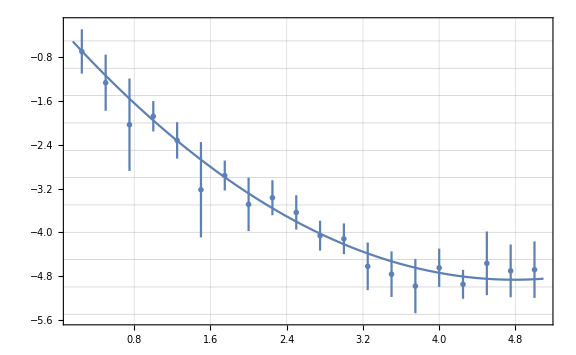
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
GridLines->{Automatic,Range[-7,0,0.5]}
]
```

#### Option: FileSave

FileSave tut was der Name sagt, es speichert euren Plot in eine Datei.
Dabei versucht es erst, es in den selben Pfad zu speichern wo sich das geladenen Notebook gerade befindet - geht das nicht, dann der Desktop - geht das nicht, dann im standardordner (unter Windows: “meine Dokumente”).
(Man achte auf den Text unter der Auswertebox)

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
FileSave->"Test.pdf"
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
C:\Users\kevin\Documents\GitHub\groenkek\HUPP\HUPP\Documentation\English\Tutorials\Test.pdf |

#### Option: Units

In eine Legende gehören, wenn möglich, auch Einheiten hinter die Parameterabschätzungen.
Das geht mit der Units Option:

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
Units->{"m^2","°","A"}
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

#### Optionen: ExtraPlots & ExtraLegends

Manchmal will man noch weitere Plots oder grafiken in den Plot mit einbringen, dafür ist ExtraPlots da der eine Liste an Graphics übernimmt.
ExtraLegends fügt an eure Legende weitere Dinge an, man beachte, dass die Legende mit einer Grid formatiert wird und man die Option dementsprechend formatieren muss.
man achte darauf, dass bei ExtraPlots auch immer die PlotRange’s eingestellt werden.

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
ExtraLegends->{{"Test"},{Style[Sqrt[x^2],{FontSize->15,FontColor->Orange}]},{LineLegend[{Red},{"BlaBlaBlabla"}]}},
ExtraPlots->{Plot[Sin[x*3]-4,{x,0,6},PlotStyle->Gray],RegionPlot[ImplicitRegion[Sqrt[(x-2.5)^2+(y+4)^2]<1.5,{x,y}],PlotRange->{{0,5},{-10,0}}],Graphics[{Red,Dashed,InfiniteLine[{{0,-6},{5,0}}]}]}
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

#### Option: Analyze

Der FitPlot Befehl, kann tatsächlcih diese ganze Auswertung überspringen aber anders als die anderen Befehle, steht diese Option standardmäßig auf True.
Bei False gibt der Befehl die FittedModelObjekte und die Grafik allein zurück.

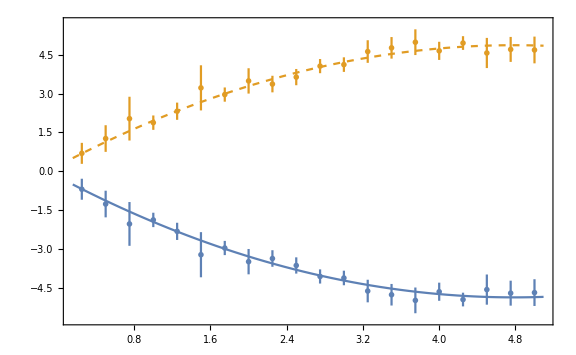
{{FittedModel[-0.212007-1.94485 x+0.203104 x^2],FittedModel[0.212007+1.94485 x-0.203104 x^2]},-Graphics-}

```mathematica
FitPlot[{data,{1,-1}*#&/@data},{yErrors,yErrors},a*x^2+b*x+c,x,
Analyze->False
]
```

#### Optionen: RSquaredTest & ChiSquareTest

Der R^2 Test wird sowieso nur bei linearen Regressionen angezeigt aber manchmal möchte man z.B. den χ^2/dof Test ausschalten da man nur relative Gewichtungen hat o.Ä.
Dafür gibt es die beiden Optionen RSquaredTest & ChiSquareTest

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
RSquaredTest->False,
ChiSquareTest->False
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

#### Option: PlotMarkerSize

FitPlot unterstützt verschiedene PlotMarker und kann deren größe verändern wenn notwendig. (Beispielsweise verkleinern bei sehr vielen Punkten)
Die normale Größe ist 6

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotMarkerSize->10
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

Oder verkleinert :

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotMarkerSize->3
]
```

regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

#### Das I, C, K Problem

FitPlot analysiert eure Gleichungen und arbeitet intern mit ihnen dabei kann es zu problemen mit drei beliebten Variablennamen kommen,
I, C und K. Alle drei haben eine Definition innerhalb von Mathematica und können deshalb nicht so einfach benutzt werden. FitPlot erkennt aber wenn ihr versucht sie zu nutzen
und führt eine Scheinvariable ein und trägt die Änderungen in der ParameterNames-Option automatisch ein. Das kann auf den ersten Blick allerdings komisch wirken, lasst euch davon nicht erschrecken.

```mathematica
FitPlot[data,yErrors,I*x^2+K*x+C,x]
```

regression | 
equation | {C543+I542 x^2+K544 x,C+I x^2+K x}
parameters |  | value | error | p-value | 
C543 | -0.212007 | 0.147581 | 0.168994 | C
K544 | -1.94485 | 0.123981 | 1.51876×10^-11 | K
I542 | 0.203104 | 0.0230933 | 9.81849×10^-8 | I
model-object | FittedModel[-0.212007-1.94485 x+0.203104 x^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | C543 | K544 | I542 | 
C543 | 1. | -0.909821 | 0.804148 | C
K544 | -0.909821 | 1. | -0.969961 | K
I542 | 0.804148 | -0.969961 | 1. | I
 | C | K | I | 
covariances |  | C543 | K544 | I542 | 
C543 | 0.0217801 | -0.0166472 | 0.00274064 | C
K544 | -0.0166472 | 0.0153714 | -0.00277714 | K
I542 | 0.00274064 | -0.00277714 | 0.000533301 | I
 | C | K | I | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

Oder für die Fitvariable

```mathematica
FitPlot[data,yErrors,a*C^2+b*C+c,C]
```

regression | 
equation | {a C549^2+b C549+c,a C^2+b C+c}
parameters |  | value | error | p-value | 
c | -0.212007 | 0.147581 | 0.168994 | c
b | -1.94485 | 0.123981 | 1.51876×10^-11 | b
a | 0.203104 | 0.0230933 | 9.81849×10^-8 | a
model-object | FittedModel[-0.212007-1.94485 C549+0.203104 C549^2]
{χ^2/dof,α} | {0.218831,0.639932}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982286,0.980202}
{86.6905,85.9294}
correlations |  | c | b | a | 
c | 1. | -0.909821 | 0.804148 | c
b | -0.909821 | 1. | -0.969961 | b
a | 0.804148 | -0.969961 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0217801 | -0.0166472 | 0.00274064 | c
b | -0.0166472 | 0.0153714 | -0.00277714 | b
a | 0.00274064 | -0.00277714 | 0.000533301 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

Aber auch das ist nicht die Lösung schlechthin. Die Variable I kann immernoch nicht in z.B. Quadrattermen auftauchen, da Mathematica automatisch I^2=-1  macht.
Um das zu entgehen, kann das Package eingepackte Zeichenketten weiterverarbeiten. 
Beispielsweise für I:

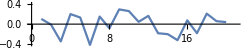
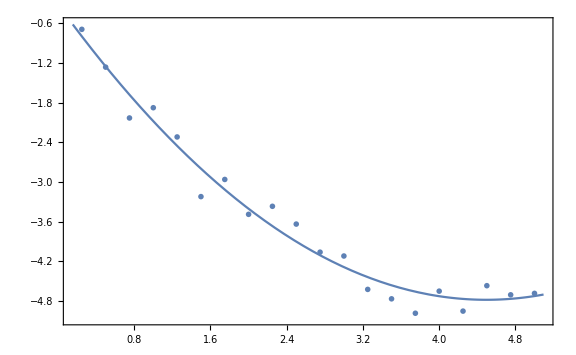
regression | 
equation | {a I554^2+b I554+c,a I^2+b I+c}
parameters |  | value | error | p-value | 
c | -0.315796 | 0.167997 | 0.0773899 | c
b | -1.9866 | 0.147377 | 1.66627×10^-10 | b
a | 0.220969 | 0.0272675 | 3.06128×10^-7 | a
model-object | FittedModel[-0.315796-1.9866 I554+0.220969 I554^2]
{χ^2/dof,α} | {0.0509891,0.821351}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.973416,0.970289}
{83.6955,82.7631}
correlations |  | c | b | a | 
c | 1. | -0.888805 | 0.781116 | c
b | -0.888805 | 1. | -0.971348 | b
a | 0.781116 | -0.971348 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0282229 | -0.0220058 | 0.00357819 | c
b | -0.0220058 | 0.02172 | -0.00390347 | b
a | 0.00357819 | -0.00390347 | 0.000743519 | a
 | c | b | a | 
residuals | -Graphics- | -Graphics-
not saved (no file specified) |

```mathematica
FitPlot[data,a*"I"^2+b*"I"+c,"I"]
```

More About

Related Tutorials

Related Wolfram Education Group Courses